# A Quantum-Like for the International Interaction Game

## The International Interaction Backward Induction Model

Explain here the Signorino  tree based model

## A Quantum-Like Approach

### Normal form approach

We propose we can understand IIG as the sequence of two normal-form game - demands and crisis games
In each of these two game, both actors have a strategic set of two strategies, from which they choose simultaneously

demands game | D2 | nD2
D1 | crisis game | U1Acq2, U2Acq2
nD1 | U1Acq1, U2Acq1 | U1SQ, U2SQ

 crisis game  | F2 | nF2
F1 | U1War, U2War | U1Cap2, U2Cap2
nF1 | U1Cap1, U2Cap1 | U1Nego, U2Nego
(we need to deal with the fact that we do not distinguish utilities of War1 and War2 in normal form game - we currently use an average of the two)

we take Signorino formula for the conditional probability of choosing between the strategies given their utilities and the expected strategy of the other player
p(F1|F2) = exp(lambda*U1War)/(exp(lambda*U1War)+exp(lambda*U1Cap1))

which results in following probability amplitudes

```mathematica
(* for debugging *)
(* U1SQ=-0.23801; U1Acq2=1.025024; U1Acq1=-1.36844;U1Nego=-1.10122; U1Cap1=-2.25679; U1Cap2=1.051597;U1War1=-1.51882; U1War2=-1.963;
U2SQ = -0.57593; U2Acq2 = -1.51157; U2Acq1=0.627684;U2Nego=0.591662; U2Cap1=0.861688; U2Cap2=-1.52841;U2War1 = 0.808828; U2War2=0.817247;
λ = 1; *)
```

```mathematica
(* U1War = Mean[{U1War1,U1War2}]; 
U2War = Mean[{U2War1,U2War2}]; *)
```

```mathematica
(* =====CRISIS GAME AMPLITUDE FUNCTIONS=====*)
(*Player 1's amplitude for fighting after Player 2 fights*)
```

```mathematica
aF1afterF2[U1War_,U1Cap1_,λ_,θ1a_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U1War);
denominator=E^(λ U1War)+E^(λ U1Cap1);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ1a]);
amplitude];

(*Player 1's amplitude for not fighting after Player 2 fights*)
aNF1afterF2[U1War_,U1Cap1_,λ_,θ1a_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U1Cap1);
denominator=E^(λ U1War)+E^(λ U1Cap1);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ1a]);
amplitude];

(*Player 1's amplitude for fighting after Player 2 doesn't fight*)
aF1afterNF2[U1Cap2_,U1Nego_,λ_,θ1b_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U1Cap2);
denominator=E^(λ U1Cap2)+E^(λ U1Nego);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ1b]);
amplitude];

(*Player 1's amplitude for not fighting after Player 2 doesn't fight*)
aNF1afterNF2[U1Cap2_,U1Nego_,λ_,θ1b_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U1Nego);
denominator=E^(λ U1Cap2)+E^(λ U1Nego);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ1b]);
amplitude];

(*Player 2's amplitude for fighting after Player 1 fights*)
aF2afterF1[U2War_,U2Cap2_,λ_,θ2a_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U2War);
denominator=E^(λ U2War)+E^(λ U2Cap2);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ2a]);
amplitude];

(*Player 2's amplitude for not fighting after Player 1 fights*)
aNF2afterF1[U2War_,U2Cap2_,λ_,θ2a_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U2Cap2);
denominator=E^(λ U2War)+E^(λ U2Cap2);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ2a]);
amplitude];

(*Player 2's amplitude for fighting after Player 1 doesn't fight*)
aF2afterNF1[U2Cap1_,U2Nego_,λ_,θ2b_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U2Cap1);
denominator=E^(λ U2Cap1)+E^(λ U2Nego);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ2b]);
amplitude];

(*Player 2's amplitude for not fighting after Player 1 doesn't fight*)
aNF2afterNF1[U2Cap1_,U2Nego_,λ_,θ2b_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U2Nego);
denominator=E^(λ U2Cap1)+E^(λ U2Nego);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ2b]);
amplitude];
```

#### Crisis Game Probability Functions

```mathematica
(*Combined amplitude for Player 1 fighting*)
aF1[pF2norm_,aF1afterF2_,aF1afterNF2_]:=(Sqrt[pF2norm]*aF1afterF2)+(Sqrt[1-pF2norm]*aF1afterNF2);

(*Probability of Player 1 fighting*)
pF1[aF1_]:=aF1*Conjugate[aF1];

(*Combined amplitude for Player 1 not fighting*)
aNF1[pF2norm_,aNF1afterF2_,aNF1afterNF2_]:=(Sqrt[pF2norm]*aNF1afterF2)+(Sqrt[1-pF2norm]*aNF1afterNF2);

(*Probability of Player 1 not fighting*)
pNF1[aNF1_]:=aNF1*Conjugate[aNF1];

(*Normalized probability of Player 1 fighting*)
pF1norm[pF1_,pNF1_]:=Module[{denominator=pF1+pNF1},If[denominator==0.,0.5,pF1/denominator] (*Avoid division by zero*)];

(*Normalized probability of Player 1 not fighting*)
pNF1norm[pF1_,pNF1_]:=Module[{denominator=pF1+pNF1},If[denominator==0.,0.5,pNF1/denominator] (*Avoid division by zero*)];

(*Combined amplitude for Player 2 fighting*)
aF2[pF1norm_,aF2afterF1_,aF2afterNF1_]:=(Sqrt[pF1norm]*aF2afterF1)+(Sqrt[1-pF1norm]*aF2afterNF1);

(*Probability of Player 2 fighting*)
pF2[aF2_]:=aF2*Conjugate[aF2];

(*Combined amplitude for Player 2 not fighting*)
aNF2[pF1norm_,aNF2afterF1_,aNF2afterNF1_]:=(Sqrt[pF1norm]*aNF2afterF1)+(Sqrt[1-pF1norm]*aNF2afterNF1);

(*Probability of Player 2 not fighting*)
pNF2[aNF2_]:=aNF2*Conjugate[aNF2];

(*Normalized probability of Player 2 fighting*)
pF2norm[pF2_,pNF2_]:=Module[{denominator=pF2+pNF2},If[denominator==0.,0.5,pF2/denominator] (*Avoid division by zero*)];

(*Normalized probability of Player 2 not fighting*)
pNF2norm[pF2_,pNF2_]:=Module[{denominator=pF2+pNF2},If[denominator==0.,0.5,pNF2/denominator] (*Avoid division by zero*)];
```

pF1 = pF2 * pF1afterF2 + pNF2 * pF1afterNF2 + 2*Sqrt[pF2*pNF2]*aF1afterF2*aF1afterNF2*Cos[θ1a-θ1b]
pF1 depends only phase difference Δθ1 = θ1a-θ1b, as expected

that gives us two equations with two variables (pF1norm, pF2norm) => unique set of pF1norm, pF2norm satisfying the conditions
in our balanced dataset, we have 375 cases (War1, War2, Cap1, Cap2, Nego) of crisis game, we can look at this stage of IIG, without combining it with demands game
we can look for what combination of Δθ1 and Δθ2 does the model has the highest fit with the empirical observations

#### Demands Game

to add the demand stage of the game (needed for the comparability to Signorino and de Mesquita), we proceed analogically to crisis game

demands game | D2 | nD2
D1 | U1Cris, U2Cris | U1Acq2, U2Acq2
nD1 | U1Acq1, U2Acq1 | U1SQ, U2SQ

```mathematica
(* U1Cris := (pF1norm*pF2norm*U1War)+(pF1norm*(1-pF2norm)*U1Cap2)+((1-pF1norm)*pF2norm*U1Cap1)+((1-pF1norm)*(1-pF2norm)*U1Nego); *)
(* U2Cris := (pF1norm*pF2norm*U2War)+(pF1norm*(1-pF2norm)*U2Cap2)+((1-pF1norm)*pF2norm*U2Cap1)+((1-pF1norm)*(1-pF2norm)*U2Nego); *)
```

```mathematica
(*Player 1's amplitude for demanding after Player 2 demands*)
aD1afterD2[U1Cris_,U1Acq1_,λ_,θ3a_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U1Cris);
denominator=E^(λ U1Cris)+E^(λ U1Acq1);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ3a]);
amplitude];

(*Player 1's amplitude for not demanding after Player 2 demands*)
aND1afterD2[U1Cris_,U1Acq1_,λ_,θ3a_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U1Acq1);
denominator=E^(λ U1Cris)+E^(λ U1Acq1);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ3a]);
amplitude];

(*Player 1's amplitude for demanding after Player 2 doesn't demand*)
aD1afterND2[U1Acq2_,U1SQ_,λ_,θ3b_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U1Acq2);
denominator=E^(λ U1Acq2)+E^(λ U1SQ);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ3b]);
amplitude];

(*Player 1's amplitude for not demanding after Player 2 doesn't demand*)
aND1afterND2[U1Acq2_,U1SQ_,λ_,θ3b_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U1SQ);
denominator=E^(λ U1Acq2)+E^(λ U1SQ);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ3b]);
amplitude];

(*Player 2's amplitude for demanding after Player 1 demands*)
aD2afterD1[U2Cris_,U2Acq2_,λ_,θ4a_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U2Cris);
denominator=E^(λ U2Cris)+E^(λ U2Acq2);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ4a]);
amplitude];

(*Player 2's amplitude for not demanding after Player 1 demands*)
aND2afterD1[U2Cris_,U2Acq2_,λ_,θ4a_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U2Acq2);
denominator=E^(λ U2Cris)+E^(λ U2Acq2);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ4a]);
amplitude];

(*Player 2's amplitude for demanding after Player 1 doesn't demand*)
aD2afterND1[U2Acq1_,U2SQ_,λ_,θ4b_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U2Acq1);
denominator=E^(λ U2Acq1)+E^(λ U2SQ);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ4b]);
amplitude];

(*Player 2's amplitude for not demanding after Player 1 doesn't demand*)
aND2afterND1[U2Acq1_,U2SQ_,λ_,θ4b_]:=Module[{numerator,denominator,amplitude},numerator=E^(λ U2SQ);
denominator=E^(λ U2Acq1)+E^(λ U2SQ);
amplitude=Sqrt[numerator/denominator]*E^(I Re[θ4b]);
amplitude];
```

```mathematica
(* =====DEMANDS GAME PROBABILITY FUNCTIONS=====*)
```

```mathematica
(*Combined amplitude for Player 1 demanding*)
aD1[pD2norm_,aD1afterD2_,aD1afterND2_]:=(Sqrt[pD2norm]*aD1afterD2)+(Sqrt[1-pD2norm]*aD1afterND2);

(*Probability of Player 1 demanding*)
pD1[aD1_]:=aD1*Conjugate[aD1];

(*Combined amplitude for Player 1 not demanding*)
aND1[pD2norm_,aND1afterD2_,aND1afterND2_]:=(Sqrt[pD2norm]*aND1afterD2)+(Sqrt[1-pD2norm]*aND1afterND2);

(*Probability of Player 1 not demanding*)
pND1[aND1_]:=aND1*Conjugate[aND1];

(*Normalized probability of Player 1 demanding*)
pD1norm[pD1_,pND1_]:=Module[{denominator=pD1+pND1},If[denominator==0.,0.5,pD1/denominator] ];

(*Normalized probability of Player 1 not demanding*)
pND1norm[pD1_,pND1_]:=Module[{denominator=pD1+pND1},If[denominator==0.,0.5,pND1/denominator] ];

(*Combined amplitude for Player 2 demanding*)
aD2[pD1norm_,aD2afterD1_,aD2afterND1_]:=(Sqrt[pD1norm]*aD2afterD1)+(Sqrt[1-pD1norm]*aD2afterND1);

(*Probability of Player 2 demanding*)
pD2[aD2_]:=aD2*Conjugate[aD2];

(*Combined amplitude for Player 2 not demanding*)
aND2[pD1norm_,aND2afterD1_,aND2afterND1_]:=(Sqrt[pD1norm]*aND2afterD1)+(Sqrt[1-pD1norm]*aND2afterND1);

(*Probability of Player 2 not demanding*)
pND2[aND2_]:=aND2*Conjugate[aND2];

(*Normalized probability of Player 2 demanding*)
pD2norm[pD2_,pND2_]:=Module[{denominator=pD2+pND2},If[denominator==0.,0.5,pD2/denominator] ];

(*Normalized probability of Player 2 not demanding*)
pND2norm[pD2_,pND2_]:=Module[{denominator=pD2+pND2},If[denominator==0.,0.5,pND2/denominator] ];
```

now there are 4 phases which we can to solve for to find the best fit with the empirical observations
Δθ1 ... phase connected to the decision to “fight/not fight” of the 1st player
Δθ2 ... phase connected to the decision to “fight/not fight” of the 2nd player
Δθ3 ... phase connected to the decision to “demand/not demand” of the 1st player
Δθ4 ... phase connected to the decision to “demand/not demand” of the 2nd player

we can set Δθ1=Δθ3 and Δθ2=Δθ4 if necessary

## Functions

### FindCrisisEquilibrium

```mathematica
(*
FindCrisisEquilibrium:
  Finds the equilibrium probabilities for the crisis game given utility values and phase differences between quantum states.
Parameters:
	 -u1War,u1Cap1,u1Cap2,u1Nego:Player 1's utilities for different outcomes
	-u2War,u2Cap2,u2Cap1,u2Nego:Player 2's utilities for different outcomes
	-lambda:Decision parameter controlling rationality (higher=more rational)
	-deltaTheta1,deltaTheta2:Phase differences for Players 1 and 2
	-maxIter:Maximum number of iterations for convergence
	-tolerance:Convergence threshold
  -verbose:Whether to record detailed iteration history
*)

FindCrisisEquilibrium[u1War_,u1Cap1_,u1Cap2_,u1Nego_,u2War_,
				      u2Cap2_,u2Cap1_,u2Nego_,
				      lambda_,deltaTheta1_,deltaTheta2_,
				      maxIter_:100,tolerance_:10^-6,
				      verbose_:False]:=
Module[{
pF1normCurrent=0.5,
pF2normCurrent=0.5,
pF1normNext,
pF2normNext,
a1F2,a1NF2,a1F1,a1NF1,p1F1,p1NF1,
a2F1,a2NF1,a2F2,a2NF2,p2F2,p2NF2,
theta1a,theta1b,theta2a,theta2b,
pWar,pCap2,pCap1,pNego,
iter=0,converged=False,
iterationHistory={},
totalProb},

(*Set phase differences*)
theta1a=deltaTheta1/2;
theta1b=-deltaTheta1/2;
theta2a=deltaTheta2/2;
theta2b=-deltaTheta2/2;

(*Initial probabilities*)
pWar=Re[pF1normCurrent*pF2normCurrent];
pCap2=Re[pF1normCurrent*(1-pF2normCurrent)];
pCap1=Re[(1-pF1normCurrent)*pF2normCurrent];
pNego=Re[(1-pF1normCurrent)*(1-pF2normCurrent)];

(*Keep a log for debugging purposes*)
If[verbose,
AppendTo[iterationHistory,
<|
"Iteration"->0,
"pF1"->Re[pF1normCurrent],
"pF2"->Re[pF2normCurrent],
"theta1a"->theta1a,
"theta1b"->theta1b,
"deltaTheta1"->deltaTheta1,
"theta2a"->theta2a,
"theta2b"->theta2b,
"deltaTheta2"->deltaTheta2,
"pWar"->Re[pWar],
"pCap2"->Re[pCap2],
"pCap1"->Re[pCap1],
"pNego"->Re[pNego],
"TotalProb"->pWar+pCap2+pCap1+pNego
|>
]
];

While[iter<maxIter&&!converged,

(*Calculate amplitudes for player 1*)
a1F2=aF1afterF2[u1War,u1Cap1,lambda,theta1a];
a1NF2=aNF1afterF2[u1War,u1Cap1,lambda,theta1a];
a1F1=aF1[pF2normCurrent,a1F2,aF1afterNF2[u1Cap2,u1Nego,lambda,theta1b]];
a1NF1=aNF1[pF2normCurrent,a1NF2,aNF1afterNF2[u1Cap2,u1Nego,lambda,theta1b]];
p1F1=pF1[a1F1];
p1NF1=pNF1[a1NF1];
pF1normNext=pF1norm[p1F1,p1NF1];

(*Calculate amplitudes for player 2*)
a2F1=aF2afterF1[u2War,u2Cap2,lambda,theta2a];
a2NF1=aNF2afterF1[u2War,u2Cap2,lambda,theta2a];
a2F2=aF2[pF1normCurrent,a2F1,aF2afterNF1[u2Cap1,u2Nego,lambda,theta2b]];
a2NF2=aNF2[pF1normCurrent,a2NF1,aNF2afterNF1[u2Cap1,u2Nego,lambda,theta2b]];
p2F2=pF2[a2F2];
p2NF2=pNF2[a2NF2];
pF2normNext=pF2norm[p2F2,p2NF2];

(*Calculate outcome probabilities*)
pWar=Re[pF1normCurrent*pF2normCurrent];
pCap2=Re[pF1normCurrent*(1-pF2normCurrent)];
pCap1=Re[(1-pF1normCurrent)*pF2normCurrent];
pNego=Re[(1-pF1normCurrent)*(1-pF2normCurrent)];

(*Check total probability for consistency*)
totalProb=pWar+pCap2+pCap1+pNego;
If[Abs[totalProb-1.0]>10^-10,
Print["Warning: Total probability differs from 1.0: ",totalProb];
];

(*Calculate convergence before updating values*)
converged=
Abs[pF1normNext-pF1normCurrent]<tolerance&&
Abs[pF2normNext-pF2normCurrent]<tolerance;

(*Track iteration if verbose*)
If[verbose,
AppendTo[iterationHistory,
<|
"Iteration"->iter,
"pF1"->Re[pF1normCurrent],
"pF2"->Re[pF2normCurrent],
"theta1a"->theta1a,
"theta1b"->theta1b,
"deltaTheta1"->deltaTheta1,
"theta2a"->theta2a,
"theta2b"->theta2b,
"deltaTheta2"->deltaTheta2,
"DeltapF1"->Abs[pF1normNext-pF1normCurrent],
"DeltapF2"->Abs[pF2normNext-pF2normCurrent],
"pWar"->pWar,
"pCap2"->pCap2,
"pCap1"->pCap1,
"pNego"->pNego,
"TotalProb"->totalProb|>
]
];

(*Update for next iteration*)
pF1normCurrent=Re[pF1normNext];
pF2normCurrent=Re[pF2normNext];
iter++;];

(*Return equilibrium probabilities and outcomes*)
<|
"Converged"->converged,
"Iterations"->iter,
"pF1"->Re[pF1normCurrent],
	"pF2"->Re[pF2normCurrent],
	"pWar"->pWar,
	"pCap2"->pCap2,
	"pCap1"->pCap1,
	"pNego"->pNego,
	"TotalProb"->totalProb,
	"IterationHistory"->If[verbose,iterationHistory,Null]
|>
];
```

### FindFullEquilibrium

```mathematica
(*
   FindFullEquilibrium:Finds the equilibrium for the full game (demands+crisis) given utility values and phase differences.
Parameters:
	 -u1War,u1Cap1,u1Cap2,u1Nego,u1SQ,u1Acq1,u1Acq2:Player 1's utilities
	-u2War,u2Cap2,u2Cap1,u2Nego,u2SQ,u2Acq1,u2Acq2:Player 2's utilities
	-lambda:Decision parameter
	-deltaTheta1,deltaTheta2:Phase differences for crisis game
	-deltaTheta3,deltaTheta4:Phase differences for demands game
	-maxIter:Maximum iterations
	-tolerance:Convergence threshold
  -verbose:Detailed logging
*)
FindFullEquilibrium[
u1War_,u1Cap1_,u1Cap2_,u1Nego_,u1SQ_,
u1Acq1_,u1Acq2_,u2War_,u2Cap2_,u2Cap1_,
u2Nego_,u2SQ_,u2Acq1_,u2Acq2_,
lambda_,
deltaTheta1_,deltaTheta2_,deltaTheta3_,deltaTheta4_,
maxIter_:100,
tolerance_:10^-6,
verbose_:False
]:=
	Module[{
	crisisEq,u1Cris,u2Cris,
	pD1normCurrent=0.5,pD2normCurrent=0.5,
	pD1normNext,pD2normNext,
	a1D2,a1ND2,a1D1,a1ND1,p1D1,p1ND1,
	a2D1,a2ND1,a2D2,a2ND2,p2D2,p2ND2,
	crisisPWar,crisisPCap1,crisisPCap2,crisisPNego,
	theta3a,theta3b,theta4a,theta4b,
	pCrisis,pAcq2,pAcq1,pSQ,totalProb,
	iter=0,converged=False,iterationHistory={}
},

(*Set phase differences for demands game*)
theta3a=deltaTheta3/2;
theta3b=-deltaTheta3/2;
theta4a=deltaTheta4/2;
theta4b=-deltaTheta4/2;

(*First find crisis game equilibrium*)
crisisEq=FindCrisisEquilibrium[
			u1War,u1Cap1,u1Cap2,u1Nego,u2War,u2Cap2,u2Cap1,u2Nego,
			lambda,deltaTheta1,deltaTheta2,maxIter,tolerance,verbose
];

(*Check if crisis game converged*)
If[!crisisEq["Converged"],
If[verbose,Print["Warning: Crisis game did not converge."]];
];

(*Extract the individual probability values*)
crisisPWar=crisisEq["pWar"];
crisisPCap1=crisisEq["pCap1"];
crisisPCap2=crisisEq["pCap2"];
crisisPNego=crisisEq["pNego"];

(*Calculate expected crisis utilities*)
u1Cris=crisisPWar*u1War+crisisPCap2*u1Cap2+crisisPCap1*u1Cap1+crisisPNego*u1Nego;
u2Cris=crisisPWar*u2War+crisisPCap2*u2Cap2+crisisPCap1*u2Cap1+crisisPNego*u2Nego;

(*Handle extreme utility values with numerical safeguards*)
If[Abs[u1Cris]>100||Abs[u2Cris]>100,
If[verbose,Print["Warning: Very high crisis utilities may cause numerical instability"]];
];

(*Initialize demand game probabilities*)
pCrisis=Re[pD1normCurrent*pD2normCurrent];
pAcq2=Re[pD1normCurrent*(1-pD2normCurrent)];
pAcq1=Re[(1-pD1normCurrent)*pD2normCurrent];
pSQ=Re[(1-pD1normCurrent)*(1-pD2normCurrent)];
totalProb=pCrisis+pAcq2+pAcq1+pSQ;

(*Record initial state if verbose*)
If[verbose,
AppendTo[iterationHistory,
<|
"Iteration"->0,
"pD1"->Re[pD1normCurrent],
"pD2"->Re[pD2normCurrent],
"theta3a"->theta3a,
"theta3b"->theta3b,
"deltaTheta3"->deltaTheta3,
"theta4a"->theta4a,
"theta4b"->theta4b,
"deltaTheta4"->deltaTheta4,
"pCrisis"->pCrisis,
"pAcq2"->pAcq2,
"pAcq1"->pAcq1,
"pSQ"->pSQ,
"TotalProb"->totalProb
|>
]
];

(*Now find demands game equilibrium*)
While[iter<maxIter&&!converged,

(*Calculate amplitudes for player 1*)
a1D2=aD1afterD2[u1Cris,u1Acq1,lambda,theta3a];
a1ND2=aND1afterD2[u1Cris,u1Acq1,lambda,theta3a];
a1D1=aD1[pD2normCurrent,a1D2,aD1afterND2[u1Acq2,u1SQ,lambda,theta3b]];
a1ND1=aND1[pD2normCurrent,a1ND2,aND1afterND2[u1Acq2,u1SQ,lambda,theta3b]];
p1D1=pD1[a1D1];
p1ND1=pND1[a1ND1];
pD1normNext=pD1norm[p1D1,p1ND1];

(*Calculate amplitudes for player 2*)
a2D1=aD2afterD1[u2Cris,u2Acq2,lambda,theta4a];
a2ND1=aND2afterD1[u2Cris,u2Acq2,lambda,theta4a];
a2D2=aD2[pD1normCurrent,a2D1,aD2afterND1[u2Acq1,u2SQ,lambda,theta4b]];
a2ND2=aND2[pD1normCurrent,a2ND1,aND2afterND1[u2Acq1,u2SQ,lambda,theta4b]];
p2D2=pD2[a2D2];
p2ND2=pND2[a2ND2];
pD2normNext=pD2norm[p2D2,p2ND2];

(*Update outcome probabilities*)
pCrisis=Re[pD1normCurrent*pD2normCurrent];
pAcq2=Re[pD1normCurrent*(1-pD2normCurrent)];
pAcq1=Re[(1-pD1normCurrent)*pD2normCurrent];
pSQ=Re[(1-pD1normCurrent)*(1-pD2normCurrent)];
totalProb=pCrisis+pAcq2+pAcq1+pSQ;

(*Check for numerical issues*)
If[Abs[totalProb-1.0]>10^-10,
If[verbose,Print["Warning: Total probability in demands game differs from 1.0: ",totalProb]];
];

(*Check convergence*)
converged=
	Abs[pD1normNext-pD1normCurrent]<tolerance&&
       Abs[pD2normNext-pD2normCurrent]<tolerance;

(*Track iteration if verbose*)
If[verbose,
AppendTo[
iterationHistory,
<|"Iteration"->iter,
"pD1"->Re[pD1normCurrent],
"pD2"->Re[pD2normCurrent],
"theta3a"->theta3a,
"theta3b"->theta3b,
"deltaTheta3"->deltaTheta3,
"theta4a"->theta4a,
"theta4b"->theta4b,
"deltaTheta4"->deltaTheta4,
"DeltapD1"->Abs[pD1normNext-pD1normCurrent],
"DeltapD2"->Abs[pD2normNext-pD2normCurrent],
"pCrisis"->pCrisis,
"pAcq2"->pAcq2,
"pAcq1"->pAcq1,
"pSQ"->pSQ,
"TotalProb"->totalProb
|>
]
];

(*Update for next iteration*)
pD1normCurrent=Re[pD1normNext];
pD2normCurrent=Re[pD2normNext];
iter++;
];

(*Return full equilibrium probabilities and outcomes*)
<|
"CrisisEquilibrium"->
<|
"pWar"->crisisPWar,
"pCap1"->crisisPCap1,
"pCap2"->crisisPCap2,
"pNego"->crisisPNego,
"pF1"->crisisEq["pF1"],
"pF2"->crisisEq["pF2"],
"Converged"->crisisEq["Converged"],
"Iterations"->crisisEq["Iterations"],
"TotalProb"->crisisEq["TotalProb"]
|>,
"DemandsConverged"->converged,
"DemandsIterations"->iter,
"pD1"->Re[pD1normCurrent],
"pD2"->Re[pD2normCurrent],
"pCrisis"->pCrisis,
"pAcq2"->pAcq2,
"pAcq1"->pAcq1,
"pSQ"->pSQ,
"TotalProb"->totalProb,
"ExpectedUtility1"->pCrisis*u1Cris+pAcq2*u1Acq2+pAcq1*u1Acq1+pSQ*u1SQ,
"ExpectedUtility2"->pCrisis*u2Cris+pAcq2*u2Acq2+pAcq1*u2Acq1+pSQ*u2SQ,
"DemandsIterationHistory"->If[verbose,iterationHistory,Null]
|>
];
```

### FindOptimalThetas

```mathematica
FindOptimalPhases[dataSet_,lambda_,
			      phaseGridSize_:10,optimizationMethod_:"GridSearch",numRandomSamples_:100,
			     maxIter_:100,threshold_:10^-6, verbose_:False]:=
Module[{
phaseValues,bestAccuracy=-Infinity,bestPhases,currentAccuracy,
results,deltaTheta1,deltaTheta2,deltaTheta3,deltaTheta4,
numToTest,statusCounter,correctCount,totalCount,outcomes,
predictions,groundtruths,safeFindEquilibrium},

(*Encapsulated function for a Safe wrapper for FindFullEquilibrium that catches errors*)
safeFindEquilibrium[u1War_,u1Cap1_,u1Cap2_,u1Nego_,
				   u1SQ_,u1Acq1_,u1Acq2_,u2War_,
				   u2Cap2_,u2Cap1_,u2Nego_,u2SQ_,
				  u2Acq1_,u2Acq2_,dt1_,dt2_,dt3_,dt4_]:=
	Module[{result},
	result=Check[
			FindFullEquilibrium[u1War,u1Cap1,u1Cap2,u1Nego,
							      u1SQ,u1Acq1,u1Acq2,u2War,
							      u2Cap2,u2Cap1,u2Nego,u2SQ,
							      u2Acq1,u2Acq2,
							      lambda,dt1,dt2,dt3,dt4,
								maxIter,threshold,verbose],
		$Failed,{Power::infy,Infinity::indet,General::stop}
     ];
result
];

(*Create grid of phase values*)
phaseValues=Table[N[2 Pi*i/phaseGridSize],{i,0,phaseGridSize-1}];

(*Determine method and number of tests*)
If[optimizationMethod=="GridSearch",

(*Grid search-test all combinations of 4 phases*)
numToTest=phaseGridSize^4;

If[numToTest>10000,
Print["Warning: Grid search will test ",numToTest," combinations. This may take a long time."];
];

(*For each combination of phases*)
statusCounter=0;
Do[

statusCounter++;

(*Update progress every 5%*)
If[Mod[statusCounter,Max[1,Round[numToTest/20]]]==0,
   Print["Progress: ",Round[100.0*statusCounter/numToTest],"% complete"];];

(*Get equilibrium for all cases in dataset with these phase parameters*)
results=Table[With[
			{row=dataSet[[i]]},
			   safeFindEquilibrium[row["U1War"],row["U1Cap1"],row["U1Cap2"],row["U1Nego"],
								row["U1SQ"],row["U1Acq1"],row["U1Acq2"],row["U2War"],
								row["U2Cap2"],row["U2Cap1"],row["U2Nego"],row["U2SQ"],
								row["U2Acq1"],row["U2Acq2"],
								deltaTheta1,deltaTheta2,deltaTheta3,deltaTheta4]],
			    {i,Length[dataSet]}
];

(*Skip this parameter combination if any calculations failed*)
If[Count[results,
$Failed]>0,
Continue[]];

(*Calculate predictions and groundtruths*)
predictions={};
groundtruths={};
Do[With[
	{row=dataSet[[i]],result=results[[i]]},
	If[result===$Failed,Continue[],(*Skip failed results*)

Module[{prediction},
Try[
(*Compute outcome probabilities*)
outcomes=
<|
"TotalOutcomes"->
<|
	"War1"->result["pCrisis"]*result["CrisisEquilibrium"]["pWar"],
	"Cap1"->result["pCrisis"]*result["CrisisEquilibrium"]["pCap1"],
	"Cap2"->result["pCrisis"]*result["CrisisEquilibrium"]["pCap2"],
	"Nego"->result["pCrisis"]*result["CrisisEquilibrium"]["pNego"],
	"Acq1"->result["pAcq1"],"Acq2"->result["pAcq2"],"SQ"->result["pSQ"]
|>
|>;

(*Get prediction*)
prediction=
First@MaximalBy[{"War1","Cap1","Cap2","Nego","Acq1","Acq2","SQ"},
				outcomes["TotalOutcomes"][#]&];
(*Add to lists*)
AppendTo[predictions,prediction];
AppendTo[groundtruths,row["groundtruth"]];]]]],{i,Length[dataSet]}];

(*Skip if we couldn't make predictions*)
If[Length[predictions]==0,Continue[]];

(*Calculate accuracy*)
correctCount=Count[Table[predictions[[i]]==groundtruths[[i]],{i,Length[predictions]}],True];
totalCount=Length[predictions];
currentAccuracy=N[correctCount/totalCount];

(*Update best fit*)
If[currentAccuracy>bestAccuracy,
bestAccuracy=currentAccuracy;
bestPhases={deltaTheta1,deltaTheta2,deltaTheta3,deltaTheta4};
Print["New best accuracy found: ",
	bestAccuracy," (",
	correctCount," correct out of ",totalCount,") with phases: ",bestPhases];
],

{deltaTheta1,phaseValues},{deltaTheta2,phaseValues},{deltaTheta3,phaseValues},{deltaTheta4,phaseValues}
],(* end Do loop *)

(*Random sampling strategy*)
Print["Using random sampling strategy with ",numRandomSamples," samples"];

	Do[
(*Randomly sample phase differences*)
deltaTheta1=RandomReal[{0,2 Pi}];
deltaTheta2=RandomReal[{0,2 Pi}];
deltaTheta3=RandomReal[{0,2 Pi}];
deltaTheta4=RandomReal[{0,2 Pi}];

(*Report progress*)
If[Mod[i,Max[1,Round[numRandomSamples/10]]]==0,
Print["Progress: ",Round[100.0*i/numRandomSamples],"% complete"];
];

(*Calculate results for each data point*)
results=
Table[
With[{row=dataSet[[j]]},
	safeFindEquilibrium[
			row["U1War"],row["U1Cap1"],row["U1Cap2"],row["U1Nego"],
			row["U1SQ"],row["U1Acq1"],row["U1Acq2"],row["U2War"],
			row["U2Cap2"],row["U2Cap1"],row["U2Nego"],row["U2SQ"],
			row["U2Acq1"],row["U2Acq2"],
			deltaTheta1,deltaTheta2,deltaTheta3,deltaTheta4]],
	{j,Length[dataSet]}];

(*Skip if any calculations failed*)
If[Count[results,$Failed]>0,Continue[]];

(*Make predictions and compare with groundtruth*)
predictions={};
groundtruths={};
Do[With[
{row=dataSet[[j]],result=results[[j]]},
If[result===$Failed,Continue[],

Module[{prediction},
Try[
(*Compute outcome probabilities*)
outcomes=<|
"TotalOutcomes"-><|"War1"->result["pCrisis"]*result["CrisisEquilibrium"]["pWar"],
"Cap1"->result["pCrisis"]*result["CrisisEquilibrium"]["pCap1"],"Cap2"->result["pCrisis"]*result["CrisisEquilibrium"]["pCap2"],
"Nego"->result["pCrisis"]*result["CrisisEquilibrium"]["pNego"],
"Acq1"->result["pAcq1"],
"Acq2"->result["pAcq2"],
"SQ"->result["pSQ"]
|>
|>;

(*Get prediction*)
prediction=
First@MaximalBy[
{"War1","Cap1","Cap2","Nego","Acq1","Acq2","SQ"},outcomes["TotalOutcomes"][#]&
];

AppendTo[predictions,prediction];
AppendTo[groundtruths,row["groundtruth"]];
]
]
]
],
{j,Length[dataSet]}
];

(*Skip if no predictions were made*)
If[Length[predictions]==0,Continue[]];

(*Calculate accuracy*)
correctCount=Count[Table[predictions[[j]]==groundtruths[[j]],{j,Length[predictions]}],True];
totalCount=Length[predictions];
currentAccuracy=N[correctCount/totalCount];

(*Update best fit*)
If[currentAccuracy>bestAccuracy,bestAccuracy=currentAccuracy;
bestPhases={deltaTheta1,deltaTheta2,deltaTheta3,deltaTheta4};
Print["New best accuracy found: ",bestAccuracy," (",correctCount," correct out of ",totalCount,") with phases: ",bestPhases];],{i,1,numRandomSamples}]
]; (* end main If *)

(*Check if we found any valid phases*)
If[bestPhases==={},
Print["Warning: No valid phase combinations found. Try adjusting parameters."];
Return[
<|"BestPhases"->{},
  "Accuracy"->0, 
   "CorrectPredictions"->0,
   "TotalCases"->0,
   "Lambda"->lambda,
   "Method"->optimizationMethod
|>
];
];

(*Return best phases and accuracy*)
<|
"BestPhases"->bestPhases,
"Accuracy"->bestAccuracy,
"CorrectPredictions"->correctCount,
"TotalCases"->totalCount,
"Lambda"->lambda,
"Method"->optimizationMethod
|>
];
```

### PlotConfusionMatrix

```mathematica
PlotConfusionMatrix[results_]:=
Module[{confusionMatrix,allCategories,matrixData,accuracyByClass,
totalsByClass,plotMatrix,plotAccuracy,layout,summaryTable},

(*Extract all unique categories from groundtruth and predictions*)allCategories=Union[Cases[results,r_/;KeyExistsQ[r,"GroundtruthOutcome"]:>r["GroundtruthOutcome"]],Cases[results,r_/;KeyExistsQ[r,"PredictedOutcome"]:>r["PredictedOutcome"]]];

(*Build confusion matrix data*)confusionMatrix=Table[With[{gt=actual,pred=predicted},{actual,predicted,Count[results,r_/;r["GroundtruthOutcome"]==gt&&r["PredictedOutcome"]==pred]}],{actual,allCategories},{predicted,allCategories}];
(*Filter entries with non-zero counts for visualization*)matrixData=Select[Flatten[confusionMatrix,1],#[[3]]>0&];
(*Calculate accuracy by class*)totalsByClass=Association@Table[cat->Count[results,r_/;r["GroundtruthOutcome"]==cat],{cat,allCategories}];
accuracyByClass=Association@Table[cat->N[Count[results,r_/;r["GroundtruthOutcome"]==cat&&r["PredictedOutcome"]==cat]/Max[totalsByClass[cat],1],6],(*Using N[] to convert to decimal*){cat,allCategories}];
(*Create the confusion matrix visualization*)plotMatrix=MatrixPlot[Table[Count[results,r_/;r["GroundtruthOutcome"]==row&&r["PredictedOutcome"]==col],{row,allCategories},{col,allCategories}],FrameLabel->{{"Actual",None},{"Predicted",None}},PlotLabel->"Confusion Matrix",Epilog->Table[Text[Count[results,r_/;r["GroundtruthOutcome"]==row&&r["PredictedOutcome"]==col],{col-1,row-1}/. {0->1,0->1}],{row,Length[allCategories]},{col,Length[allCategories]}],FrameTicks->{{Table[{i,allCategories[[i]]},{i,Length[allCategories]}],None},{Table[{i,allCategories[[i]]},{i,Length[allCategories]}],None}},ColorFunction->(ColorData["TemperatureMap"][#]&),PlotLegends->BarLegend[{"TemperatureMap",{0,Max[Cases[matrixData,{_,_,count_}:>count]]}},LegendLabel->"Count"]];
(*Create class accuracy bar chart*)plotAccuracy=BarChart[Values[accuracyByClass],ChartLabels->Keys[accuracyByClass],PlotLabel->"Accuracy by Class",AxesLabel->{"Class","Accuracy"},PlotRange->{0,1},GridLines->Automatic,ChartStyle->"Pastel",LabelingFunction->(Placed[NumberForm[#,{4,4}],Above]&)  (*Changed to 4 decimal places*)];
(*Create textual summary with decimal values instead of fractions*)summaryTable=Grid[Prepend[Table[{cat,totalsByClass[cat],Count[results,r_/;r["PredictedOutcome"]==cat],Count[results,r_/;r["GroundtruthOutcome"]==cat&&r["PredictedOutcome"]==cat],NumberForm[accuracyByClass[cat],{4,4}]  (*Changed to 4 decimal places*)},{cat,allCategories}],{"Category","Actual Count","Predicted Count","Correct","Accuracy"}],Frame->All,Background->{None,{LightGray,None}},Alignment->{Left,Center}];
(*Return visualizations in a column*)Column[{plotMatrix,plotAccuracy,summaryTable,Style["Overall Accuracy: "<>ToString[NumberForm[N[Count[results,r_/;r["GroundtruthOutcome"]==r["PredictedOutcome"]]/Max[Length[results],1],6],{4,4}  (*Changed to 4 decimal places*)]],Bold]},Spacings->1]];
```

### PrepareDataset

```mathematica
(*PrepareDataset:Transforms raw data into the format needed for model analysis*)
```

```mathematica
PrepareDataset[dataset_]:=Table[<|"Agent1"->dataset[i,"Agent1"],"Agent2"->dataset[i,"Agent2"],"U1War"->(dataset[i,"wrTu1wr1"]+dataset[i,"wrTu1wr2"])/2,"U1Cap1"->dataset[i,"wrTu1cp1"],"U1Cap2"->dataset[i,"wrTu1cp2"],"U1Nego"->dataset[i,"wrTu1neg"],"U1SQ"->dataset[i,"wrTu1sq"],"U1Acq1"->dataset[i,"wrTu1ac1"],"U1Acq2"->dataset[i,"wrTu1ac2"],"U2War"->(dataset[i,"wrTu2wr1"]+dataset[i,"wrTu2wr2"])/2,"U2Cap1"->dataset[i,"wrTu2cp1"],"U2Cap2"->dataset[i,"wrTu2cp2"],"U2Nego"->dataset[i,"wrTu2neg"],"U2SQ"->dataset[i,"wrTu2sq"],"U2Acq1"->dataset[i,"wrTu2ac1"],"U2Acq2"->dataset[i,"wrTu2ac2"],"groundtruth"->dataset[i,"groundtruth"]|>,{i,Length[dataset]}];
```

### PlotCrisisConvergence

```mathematica
(*PlotCrisisConvergence:Visualizes the convergence of crisis game probabilities*)
```

```mathematica
PlotCrisisConvergence[history_]:=Module[{playerPlot,outcomePlot,convergencePlot,historyTable},(*Player fight probabilities*)playerPlot=ListPlot[{Table[{i,history[[i+1,"pF1"]]},{i,0,Length[history]-1}],Table[{i,history[[i+1,"pF2"]]},{i,0,Length[history]-1}]},PlotLegends->{"Player 1","Player 2"},AxesLabel->{"Iteration","Probability"},PlotLabel->"Convergence of Fight Probabilities",Joined->True,Mesh->All,PlotMarkers->Automatic,GridLines->Automatic,PlotRange->{0,1}];
(*Outcome probabilities*)outcomePlot=ListPlot[{Table[{i,history[[i+1,"pWar"]]},{i,0,Length[history]-1}],Table[{i,history[[i+1,"pCap2"]]},{i,0,Length[history]-1}],Table[{i,history[[i+1,"pCap1"]]},{i,0,Length[history]-1}],Table[{i,history[[i+1,"pNego"]]},{i,0,Length[history]-1}]},PlotLegends->{"pWar","pCap2","pCap1","pNego"},AxesLabel->{"Iteration","Probability"},PlotLabel->"Convergence of Probabilities in Crisis Game",Joined->True,Mesh->All,PlotMarkers->Automatic,GridLines->Automatic,PlotRange->{0,1}];
(*Convergence rate*)If[Length[history]>1,convergencePlot=ListLogPlot[{Table[{i,history[[i+1,"DeltapF1"]]},{i,1,Length[history]-1}],Table[{i,history[[i+1,"DeltapF2"]]},{i,1,Length[history]-1}]},PlotLegends->{"Player 1","Player 2"},AxesLabel->{"Iteration","Log(Δp)"},PlotLabel->"Convergence Rate",Joined->True,GridLines->Automatic],convergencePlot=Graphics[{},PlotLabel->"Insufficient data for convergence plot"]];
(*Iteration table*)If[Length[history]>1,historyTable=Grid[{{"Iteration","pF1","pF2","DeltapF1","DeltapF2","theta1a","theta1b","theta2a","theta2b","deltaTheta1","deltaTheta2"}}~Join~Table[{history[[i,"Iteration"]],NumberForm[history[[i,"pF1"]],{4,4}],NumberForm[history[[i,"pF2"]],{4,4}],If[i>1,NumberForm[history[[i,"DeltapF1"]],{4,4}],"-"],If[i>1,NumberForm[history[[i,"DeltapF2"]],{4,4}],"-"],NumberForm[history[[i,"theta1a"]],{4,4}],NumberForm[history[[i,"theta1b"]],{4,4}],NumberForm[history[[i,"theta2a"]],{4,4}],NumberForm[history[[i,"theta2b"]],{4,4}],NumberForm[history[[i,"deltaTheta1"]],{4,4}],NumberForm[history[[i,"deltaTheta2"]],{4,4}]},{i,1,Min[Length[history],10]}],Frame->All,Alignment->Center,Background->{None,{LightGray,None}}],historyTable=Grid[{{"No iteration data available"}}]];
(*Return all visualizations*){playerPlot,outcomePlot,convergencePlot,historyTable}];
```

### PlotDemandsConvergence

```mathematica
(*PlotDemandsConvergence:Visualizes the convergence of demands game probabilities*)
PlotDemandsConvergence[history_]:=Module[{playerPlot,outcomePlot,convergencePlot,historyTable},(*Player demand probabilities*)playerPlot=ListPlot[{Table[{i,history[[i+1,"pD1"]]},{i,0,Length[history]-1}],Table[{i,history[[i+1,"pD2"]]},{i,0,Length[history]-1}]},PlotLegends->{"Player 1","Player 2"},AxesLabel->{"Iteration","Probability"},PlotLabel->"Convergence of Demand Probabilities",Joined->True,Mesh->All,PlotMarkers->Automatic,GridLines->Automatic,PlotRange->{0,1}];
(*Outcome probabilities*)outcomePlot=ListPlot[{Table[{i,history[[i+1,"pCrisis"]]},{i,0,Length[history]-1}],Table[{i,history[[i+1,"pAcq2"]]},{i,0,Length[history]-1}],Table[{i,history[[i+1,"pAcq1"]]},{i,0,Length[history]-1}],Table[{i,history[[i+1,"pSQ"]]},{i,0,Length[history]-1}]},PlotLegends->{"pCrisis","pAcq2","pAcq1","pSQ"},AxesLabel->{"Iteration","Probability"},PlotLabel->"Convergence of Probabilities in Demands Game",Joined->True,Mesh->All,PlotMarkers->Automatic,GridLines->Automatic,PlotRange->{0,1}];
(*Convergence rate*)If[Length[history]>1,convergencePlot=ListLogPlot[{Table[{i,history[[i+1,"DeltapD1"]]},{i,1,Length[history]-1}],Table[{i,history[[i+1,"DeltapD2"]]},{i,1,Length[history]-1}]},PlotLegends->{"Player 1","Player 2"},AxesLabel->{"Iteration","Log(Δp)"},PlotLabel->"Demand Game Convergence Rate",Joined->True,GridLines->Automatic],convergencePlot=Graphics[{},PlotLabel->"Insufficient data for convergence plot"]];
(*Iteration table*)If[Length[history]>1,historyTable=Grid[{{"Iteration","pD1","pD2","DeltapD1","DeltapD2","theta3a","theta3b","theta4a","theta4b","deltaTheta3","deltaTheta4"}}~Join~Table[{history[[i,"Iteration"]],NumberForm[history[[i,"pD1"]],{4,4}],NumberForm[history[[i,"pD2"]],{4,4}],If[i>1,NumberForm[history[[i,"DeltapD1"]],{4,4}],"-"],If[i>1,NumberForm[history[[i,"DeltapD2"]],{4,4}],"-"],NumberForm[history[[i,"theta3a"]],{4,4}],NumberForm[history[[i,"theta3b"]],{4,4}],NumberForm[history[[i,"theta4a"]],{4,4}],NumberForm[history[[i,"theta4b"]],{4,4}],NumberForm[history[[i,"deltaTheta3"]],{4,4}],NumberForm[history[[i,"deltaTheta4"]],{4,4}]},{i,1,Min[Length[history],10]}],Frame->All,Alignment->Center,Background->{None,{LightGray,None}}],historyTable=Grid[{{"No iteration data available"}}]];
(*Return all visualizations*){playerPlot,outcomePlot,convergencePlot,historyTable}];
```

### CreateSummaryTable

```mathematica
(*Corrected CreateSummaryTable function*)(*CreateSummaryTable:Creates a summary table of outcome probabilities from the full game.This corrected version properly calculates the total probabilities by multiplying crisis game outcomes by the probability of the crisis occurring.*)CreateSummaryTable[fullResult_]:=Module[{crisisEq=fullResult["CrisisEquilibrium"],crisisProb=fullResult["pCrisis"],(*Calculate total probabilities*)totalWarProb,totalCap1Prob,totalCap2Prob,totalNegoProb,(*Calculate marginal probabilities*)marginalWarProb,marginalCap1Prob,marginalCap2Prob,marginalNegoProb},(*Get marginal probabilities (within crisis game)*)marginalWarProb=crisisEq["pWar"];
marginalCap1Prob=crisisEq["pCap1"];
marginalCap2Prob=crisisEq["pCap2"];
marginalNegoProb=crisisEq["pNego"];

(*Calculate total probabilities (accounting for crisis probability)*)totalWarProb=crisisProb*marginalWarProb;
totalCap1Prob=crisisProb*marginalCap1Prob;
totalCap2Prob=crisisProb*marginalCap2Prob;
totalNegoProb=crisisProb*marginalNegoProb;

(*Create the summary table with both marginal and total probabilities*)Grid[{{"Game Stage","Outcome","Marginal Probability","Total Probability"},{"Crisis Game","War",marginalWarProb,totalWarProb},{"Crisis Game","Capitulation 1",marginalCap1Prob,totalCap1Prob},{"Crisis Game","Capitulation 2",marginalCap2Prob,totalCap2Prob},{"Crisis Game","Negotiation",marginalNegoProb,totalNegoProb},{"Demands Game","Crisis",fullResult["pCrisis"],fullResult["pCrisis"]},{"Demands Game","Acquiescence 1",fullResult["pAcq1"],fullResult["pAcq1"]},{"Demands Game","Acquiescence 2",fullResult["pAcq2"],fullResult["pAcq2"]},{"Demands Game","Status Quo",fullResult["pSQ"],fullResult["pSQ"]}},Frame->All,Alignment->{Left,Left,Right,Right},Background->{{LightGray,None},{LightGray,None,LightGray,None,LightGray,None,LightGray,None,LightGray}},Dividers->{{None,None,{True},None},None}]];
```

### VerifyFullGameProbabilities

```mathematica
(*Function to verify that probabilities sum to 1*)
VerifyFullGameProbabilities[fullResult_]:=Module[{crisisEq=fullResult["CrisisEquilibrium"],crisisProb=fullResult["pCrisis"],totalWarProb,totalCap1Prob,totalCap2Prob,totalNegoProb,totalSum,crisisSumCheck,demandsSumCheck},(*Calculate total probabilities*)totalWarProb=crisisProb*crisisEq["pWar"];
totalCap1Prob=crisisProb*crisisEq["pCap1"];
totalCap2Prob=crisisProb*crisisEq["pCap2"];
totalNegoProb=crisisProb*crisisEq["pNego"];
(*Verify that probabilities sum to 1*)totalSum=totalWarProb+totalCap1Prob+totalCap2Prob+totalNegoProb+fullResult["pAcq1"]+fullResult["pAcq2"]+fullResult["pSQ"];
crisisSumCheck=crisisEq["pWar"]+crisisEq["pCap1"]+crisisEq["pCap2"]+crisisEq["pNego"];
demandsSumCheck=fullResult["pCrisis"]+fullResult["pAcq1"]+fullResult["pAcq2"]+fullResult["pSQ"];
<|"TotalProbabilitySum"->totalSum,"SumsToOne"->Abs[totalSum-1.0]<10^-10,"CrisisGameSum"->crisisSumCheck,"DemandsGameSum"->demandsSumCheck,"Crisis-War"->totalWarProb,"Crisis-Cap1"->totalCap1Prob,"Crisis-Cap2"->totalCap2Prob,"Crisis-Nego"->totalNegoProb,"Acquiescence 1"->fullResult["pAcq1"],"Acquiescence 2"->fullResult["pAcq2"],"Status Quo"->fullResult["pSQ"]|>];
```

### ComputeOutcomeProbabilities

```mathematica
(*ComputeOutcomeProbabilities:This function computes and organizes the probabilities of all possible outcomes based on the output of FindFullEquilibrium,using the required key naming convention:"War1","Cap1","Cap2","Nego","Acq1","Acq2","SQ" Input:-fullResult:The result from FindFullEquilibrium Output:-An association containing:-Total probabilities for all possible outcomes-Sub-game probabilities (demands game and crisis game)-Organized outcome probabilities by game stage-Verification that probabilities sum to 1*)ComputeOutcomeProbabilities[fullResult_]:=Module[{(*Extract crisis game equilibrium from the full result*)crisisEq=fullResult["CrisisEquilibrium"],(*Extract probabilities from demands game*)crisisProb=fullResult["pCrisis"],acq1Prob=fullResult["pAcq1"],acq2Prob=fullResult["pAcq2"],sqProb=fullResult["pSQ"],(*Variables to store computed probabilities*)warProb,cap1Prob,cap2Prob,negoProb,crisisSum,demandsSum,totalSum,(*Organize outcomes by type*)outcomes},(*Calculate total outcome probabilities from the crisis game*)warProb=crisisProb*crisisEq["pWar"];
cap1Prob=crisisProb*crisisEq["pCap1"];
cap2Prob=crisisProb*crisisEq["pCap2"];
negoProb=crisisProb*crisisEq["pNego"];
(*Verify probability sums*)crisisSum=crisisEq["pWar"]+crisisEq["pCap1"]+crisisEq["pCap2"]+crisisEq["pNego"];
demandsSum=crisisProb+acq1Prob+acq2Prob+sqProb;
totalSum=warProb+cap1Prob+cap2Prob+negoProb+acq1Prob+acq2Prob+sqProb;
(*Organize outcomes by type with the required key names*)outcomes=<|(*All outcomes with their total probabilities using the required key names*)"TotalOutcomes"-><|"War1"->warProb,"Cap1"->cap1Prob,"Cap2"->cap2Prob,"Nego"->negoProb,"Acq1"->acq1Prob,"Acq2"->acq2Prob,"SQ"->sqProb|>,(*Outcomes organized by game stage with the required key names*)"ByGameStage"-><|"DemandsGame"-><|"Crisis"->crisisProb,"Acq1"->acq1Prob,"Acq2"->acq2Prob,"SQ"->sqProb|>,"CrisisGame"-><|"War1"->crisisEq["pWar"],"Cap1"->crisisEq["pCap1"],"Cap2"->crisisEq["pCap2"],"Nego"->crisisEq["pNego"]|>|>,(*Player choice probabilities*)"PlayerChoices"-><|"DemandsGame"-><|"Player1Demands"->fullResult["pD1"],"Player2Demands"->fullResult["pD2"]|>,"CrisisGame"-><|"Player1Fights"->crisisEq["pF1"],"Player2Fights"->crisisEq["pF2"]|>|>,(*Verification*)"Verification"-><|"CrisisGameSumToOne"->crisisSum,"DemandsGameSumToOne"->demandsSum,"TotalProbabilitySumToOne"->totalSum,"IsValid"->Abs[totalSum-1.0]<10^-10|>|>;
(*Return the organized probabilities*)Return[outcomes];];
```

### GenerateOutcomeSummaryTable

```mathematica
GenerateOutcomeSummaryTable[outcomes_]:=Module[{rows},rows={(*Header row*){"Outcome","Type","Probability","Conditional Probability"},(*War outcome*){"War","Final Outcome",NumberForm[outcomes["TotalOutcomes"]["War1"],{4,4}],NumberForm[outcomes["ByGameStage"]["CrisisGame"]["War1"],{4,4}]},(*Capitulation outcomes*){"Capitulation by Player 1","Final Outcome",NumberForm[outcomes["TotalOutcomes"]["Cap1"],{4,4}],NumberForm[outcomes["ByGameStage"]["CrisisGame"]["Cap1"],{4,4}]},{"Capitulation by Player 2","Final Outcome",NumberForm[outcomes["TotalOutcomes"]["Cap2"],{4,4}],NumberForm[outcomes["ByGameStage"]["CrisisGame"]["Cap2"],{4,4}]},(*Negotiation outcome*){"Negotiation","Final Outcome",NumberForm[outcomes["TotalOutcomes"]["Nego"],{4,4}],NumberForm[outcomes["ByGameStage"]["CrisisGame"]["Nego"],{4,4}]},(*Acquiescence outcomes*){"Acquiescence by Player 1","Initial Outcome",NumberForm[outcomes["TotalOutcomes"]["Acq1"],{4,4}],"-"},{"Acquiescence by Player 2","Initial Outcome",NumberForm[outcomes["TotalOutcomes"]["Acq2"],{4,4}],"-"},(*Status quo outcome*){"Status Quo","Initial Outcome",NumberForm[outcomes["TotalOutcomes"]["SQ"],{4,4}],"-"},(*Verification row*){"Sum of Probabilities","Verification",NumberForm[outcomes["Verification"]["TotalProbabilitySumToOne"],{4,4}],"1.0000 (Expected)"}};
(*Create and return the formatted grid-OUTSIDE the rows definition*)Grid[rows,Frame->All,Alignment->{Left,Left,Right,Right},Background->{None,{LightGray,None,None,None,None,None,None,None,LightGray}},Dividers->{{True},{True,True,False,False,False,True,False,False,True}}]];
```

### GetMaxProbabilityOutcome

```mathematica
(*Direct,simplified version of GetMaxProbabilityOutcome*)GetMaxProbabilityOutcome[outcomes_]:=Module[{totalOutcomes,maxKey,maxVal},totalOutcomes=outcomes["TotalOutcomes"];
maxVal=-Infinity;
maxKey="";
(*Find the maximum value and its key directly*)If[totalOutcomes["Acq1"]>maxVal,maxVal=totalOutcomes["Acq1"];maxKey="Acq1"];
If[totalOutcomes["War1"]>maxVal,maxVal=totalOutcomes["War1"];maxKey="War1"];
If[totalOutcomes["Cap1"]>maxVal,maxVal=totalOutcomes["Cap1"];maxKey="Cap1"];
If[totalOutcomes["Cap2"]>maxVal,maxVal=totalOutcomes["Cap2"];maxKey="Cap2"];
If[totalOutcomes["Nego"]>maxVal,maxVal=totalOutcomes["Nego"];maxKey="Nego"];
If[totalOutcomes["Acq2"]>maxVal,maxVal=totalOutcomes["Acq2"];maxKey="Acq2"];
If[totalOutcomes["SQ"]>maxVal,maxVal=totalOutcomes["SQ"];maxKey="SQ"];
(*Return the mapped value*)Which[maxKey=="War1","War1",maxKey=="Cap1","Cap1",maxKey=="Cap2","Cap2",maxKey=="Nego","Nego",maxKey=="Acq1","Acq1",maxKey=="Acq2","Acq2",maxKey=="SQ","SQ",True,"Unknown"]];
```

### CompareWithGroundtruth

```mathematica
(*CompareWithGroundtruth:Properly compares prediction with groundtruth*)
CompareWithGroundtruth[outcomes_,groundtruth_]:=Module[{predictedOutcome,groundtruthStandard,isCorrect},(*Get the actual predicted outcome*)predictedOutcome=GetMaxProbabilityOutcome[outcomes];
(*Convert the groundtruth to standard form if needed*)groundtruthStandard=Which[groundtruth=="Cap1","Cap1",groundtruth=="Cap2","Cap2",groundtruth=="Nego","Nego",groundtruth=="Acq1","Acq1",groundtruth=="Acq2","Acq2",groundtruth=="SQ","SQ",groundtruth=="War1","War1",True,groundtruth];
(*Check if the prediction matches the groundtruth*)isCorrect=predictedOutcome==groundtruthStandard;
(*Return the comparison results*)Return[<|"PredictedOutcome"->predictedOutcome,"GroundtruthOutcome"->groundtruthStandard,"IsCorrect"->isCorrect,"AllProbabilities"->outcomes["TotalOutcomes"]|>];];
```

### GetModelMetrics

```mathematica
GetModelMetrics[preparedData_,lambda_,bestPhases_,maxIter_:100,tolerance_:10^-6,verbose_:False]:=Module[{result,outcomes,comparisonResults,allCategories,totalsByClass,correctByClass,predictedByClass,precision,recall,f1Score,accuracy,overallMetricsGrid,classMetricsGrid,confusionMatrixPlot,visualOutput},(*Run model for each data point*)comparisonResults=Table[With[{row=preparedData[[i]]},(*Run model with optimal phases*)result=FindFullEquilibrium[row["U1War"],row["U1Cap1"],row["U1Cap2"],row["U1Nego"],row["U1SQ"],row["U1Acq1"],row["U1Acq2"],row["U2War"],row["U2Cap2"],row["U2Cap1"],row["U2Nego"],row["U2SQ"],row["U2Acq1"],row["U2Acq2"],lambda,bestPhases[[1]],bestPhases[[2]],bestPhases[[3]],bestPhases[[4]],maxIter,tolerance,verbose];
(*Compute outcome probabilities*)outcomes=ComputeOutcomeProbabilities[result];
(*Compare with groundtruth*)CompareWithGroundtruth[outcomes,row["groundtruth"]]],{i,Length[preparedData]}];
(*Get all unique outcome categories*)allCategories=Union[Cases[comparisonResults,r_/;KeyExistsQ[r,"GroundtruthOutcome"]:>r["GroundtruthOutcome"]],Cases[comparisonResults,r_/;KeyExistsQ[r,"PredictedOutcome"]:>r["PredictedOutcome"]]];
(*Calculate counts for each category*)totalsByClass=Association@Table[cat->Count[comparisonResults,r_/;r["GroundtruthOutcome"]==cat],{cat,allCategories}];
correctByClass=Association@Table[cat->Count[comparisonResults,r_/;r["GroundtruthOutcome"]==cat&&r["PredictedOutcome"]==cat],{cat,allCategories}];
predictedByClass=Association@Table[cat->Count[comparisonResults,r_/;r["PredictedOutcome"]==cat],{cat,allCategories}];
(*Calculate precision,recall,and F1 score for each class*)precision=Association@Table[cat->If[predictedByClass[cat]>0,N[correctByClass[cat]/predictedByClass[cat],4],0.0],{cat,allCategories}];
recall=Association@Table[cat->If[totalsByClass[cat]>0,N[correctByClass[cat]/totalsByClass[cat],4],0.0],{cat,allCategories}];
f1Score=Association@Table[cat->If[precision[cat]+recall[cat]>0,N[2*precision[cat]*recall[cat]/(precision[cat]+recall[cat]),4],0.0],{cat,allCategories}];
(*Calculate overall accuracy*)accuracy=N[Count[comparisonResults,r_/;r["IsCorrect"]==True]/Length[comparisonResults],4];
(*Create overall metrics grid*)overallMetricsGrid=Grid[{{"Accuracy",NumberForm[accuracy,{4,4}]},{"Macro-Average Precision",NumberForm[Mean[Values[precision]],{4,4}]},{"Macro-Average Recall",NumberForm[Mean[Values[recall]],{4,4}]},{"Macro-Average F1",NumberForm[Mean[Values[f1Score]],{4,4}]},{"Weighted Average F1",NumberForm[Sum[totalsByClass[cat]/Length[comparisonResults]*f1Score[cat],{cat,allCategories}],{4,4}]}},Alignment->{Left,Right},Frame->All,Background->{None,{LightOrange,None,None,None,None}}];
(*Create per-class metrics grid*)classMetricsGrid=Grid[Prepend[Table[{cat,totalsByClass[cat],predictedByClass[cat],correctByClass[cat],NumberForm[precision[cat],{4,4}],NumberForm[recall[cat],{4,4}],NumberForm[f1Score[cat],{4,4}]},{cat,allCategories}],{"Category","Actual","Predicted","Correct","Precision","Recall","F1 Score"}],Frame->All,Background->{None,{LightGray,None,None,None,None,None,None,None}}];
(*Create confusion matrix plot*)confusionMatrixPlot=PlotConfusionMatrix[comparisonResults];
(*Compile all visuals into one display*)visualOutput=Column[{Style["Model Performance with Phases: "<>ToString[bestPhases],Bold,14],Spacer[10],Style["Overall Performance Metrics:",Bold,12],overallMetricsGrid,Spacer[20],Style["Performance by Outcome Category:",Bold,12],classMetricsGrid,Spacer[20],Style["Confusion Matrix Analysis:",Bold,12],confusionMatrixPlot},Alignment->Left,Spacings->1];
(*Display the visual output*)Print[visualOutput];
(*Return comprehensive metrics as structured data*)<|"Accuracy"->accuracy,"ClassMetrics"->Table[<|"Category"->cat,"Actual"->totalsByClass[cat],"Predicted"->predictedByClass[cat],"Correct"->correctByClass[cat],"Precision"->precision[cat],"Recall"->recall[cat],"F1Score"->f1Score[cat]|>,{cat,allCategories}],"MacroAveragePrecision"->N[Mean[Values[precision]],4],"MacroAverageRecall"->N[Mean[Values[recall]],4],"MacroAverageF1"->N[Mean[Values[f1Score]],4],"WeightedAverageF1"->N[Sum[totalsByClass[cat]/Length[comparisonResults]*f1Score[cat],{cat,allCategories}],4],"ComparisonResults"->comparisonResults|>]
```

## Testing Overall Code Functionality on Imbalanced Dataset

### Load Data

```mathematica
(* load data *)
```

```mathematica
data=Import["/Users/162191/Documents/GitHub/quantum_international_interaction_game/Norm_Form/first_dataset_with_SQ.csv","CSV","HeaderLines"->1];
dataset=Dataset[Association@@@(Rule@@@Transpose[{{"Agent1","Agent2","wrTu1sq","wrTu1ac1","wrTu1ac2","wrTu1neg","wrTu1cp1","wrTu1cp2","wrTu1wr1","wrTu1wr2","wrTu2sq","wrTu2ac2","wrTu2ac1","wrTu2neg","wrTu2cp2","wrTu2cp1","wrTu2wr2","wrTu2wr1","groundtruth"},#}]&/@data)];
```

```mathematica
Length[dataset]
```

751

### Prepare Data

```mathematica
preparedData = PrepareDataset[dataset];
sampleCase = preparedData[[7]];
groundtruth = sampleCase["groundtruth"]
```

Cap1

### Params

```mathematica
NumSamples = 2;
lambda = 1.0;
dt1 = Pi;
dt2 = 3 Pi / 2;
dt3 = Pi ;
dt4 = Pi / 2 ;
maxIter = 200;
threshold = 0.000001;
verboseMode = True;
```

### Crisis Game

```mathematica
crisisResult=FindCrisisEquilibrium[sampleCase["U1War"],
								 sampleCase["U1Cap1"],
								 sampleCase["U1Cap2"],
								 sampleCase["U1Nego"],
								 sampleCase["U2War"],
								 sampleCase["U2Cap2"],
							          sampleCase["U2Cap1"],
								 sampleCase["U2Nego"],
								 lambda,
								 dt1,
								 dt2,
								 maxIter,
								 threshold,
								 verboseMode];
```

```mathematica
(* visualise results *)
```

```mathematica
crisisConvergenceViz = PlotCrisisConvergence[crisisResult["IterationHistory"]];
```

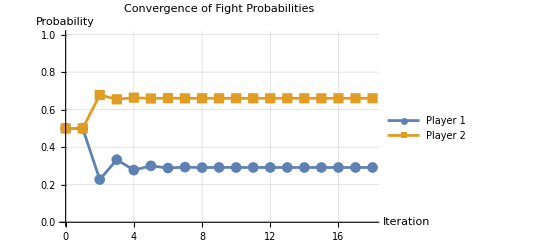

```mathematica
crisisConvergenceViz[[1]]
```

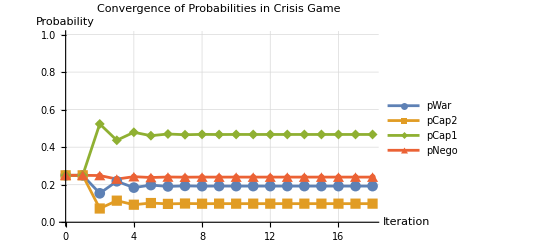

```mathematica
crisisConvergenceViz[[2]]
```

### Full Game

```mathematica
fullResult=FindFullEquilibrium[sampleCase["U1War"],
							sampleCase["U1Cap1"],
							sampleCase["U1Cap2"],
							sampleCase["U1Nego"],
							sampleCase["U1SQ"],
							sampleCase["U1Acq1"],
							sampleCase["U1Acq2"],
							sampleCase["U2War"],
							sampleCase["U2Cap2"],
							sampleCase["U2Cap1"],
							sampleCase["U2Nego"],
							sampleCase["U2SQ"],
							sampleCase["U2Acq1"],
							sampleCase["U2Acq2"],
							lambda,
							dt1,
							dt2,
							dt3,
							dt4,
							maxIter,
							threshold,
							verboseMode];
```

```mathematica
(* visualise results *)
```

```mathematica
fullGameConvergenceViz = PlotDemandsConvergence[fullResult["DemandsIterationHistory"]];
CreateSummaryTable[fullResult]
```

Game Stage | Outcome | Marginal Probability | Total Probability
Crisis Game | War | 0.192676 | 0.0580155
Crisis Game | Capitulation 1 | 0.467689 | 0.140823
Crisis Game | Capitulation 2 | 0.0990958 | 0.0298381
Crisis Game | Negotiation | 0.240539 | 0.0724271
Demands Game | Crisis | 0.301104 | 0.301104
Demands Game | Acquiescence 1 | 0.498101 | 0.498101
Demands Game | Acquiescence 2 | 0.0756504 | 0.0756504
Demands Game | Status Quo | 0.125145 | 0.125145

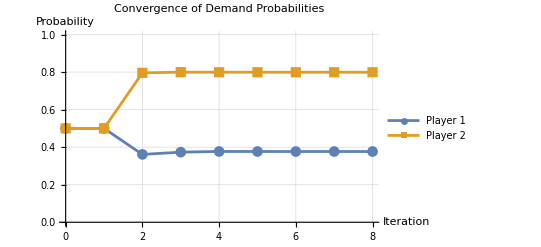

```mathematica
fullGameConvergenceViz[[1]]
```

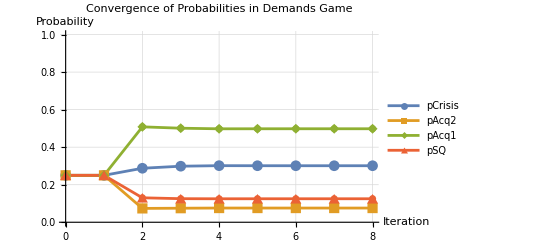

```mathematica
fullGameConvergenceViz[[2]]
```

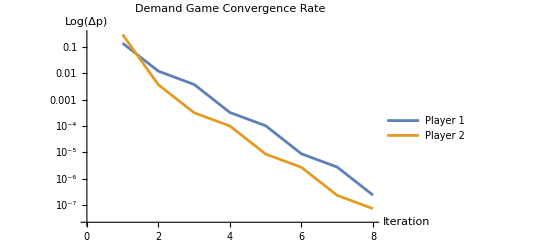

```mathematica
fullGameConvergenceViz[[3]]
```

```mathematica
VerifyFullGameProbabilities[fullResult]
```

<|TotalProbabilitySum→1.,SumsToOne→True,CrisisGameSum→1.,DemandsGameSum→1.,Crisis-War→0.0580155,Crisis-Cap1→0.140823,Crisis-Cap2→0.0298381,Crisis-Nego→0.0724271,Acquiescence 1→0.498101,Acquiescence 2→0.0756504,Status Quo→0.125145|>

```mathematica
outcomes=ComputeOutcomeProbabilities[fullResult];
```

```mathematica
summaryTable=GenerateOutcomeSummaryTable[outcomes]
```

Outcome | Type | Probability | Conditional Probability
War | Final Outcome | 0.0580 | 0.1927
Capitulation by Player 1 | Final Outcome | 0.1408 | 0.4677
Capitulation by Player 2 | Final Outcome | 0.0298 | 0.0991
Negotiation | Final Outcome | 0.0724 | 0.2405
Acquiescence by Player 1 | Initial Outcome | 0.4981 | -
Acquiescence by Player 2 | Initial Outcome | 0.0757 | -
Status Quo | Initial Outcome | 0.1251 | -
Sum of Probabilities | Verification | 1.0000 | 1.0000 (Expected)

```mathematica
(*Get the outcome with maximum probability*)
maxOutcome=GetMaxProbabilityOutcome[outcomes]
```

Acq1

```mathematica
(*Compare with groundtruth*)
comparison=CompareWithGroundtruth[outcomes,groundtruth]
```

<|PredictedOutcome→Acq1,GroundtruthOutcome→Cap1,IsCorrect→False,AllProbabilities→<|War1→0.0580155,Cap1→0.140823,Cap2→0.0298381,Nego→0.0724271,Acq1→0.498101,Acq2→0.0756504,SQ→0.125145|>|>